```mathematica
fun2= <<"E:Work_Folder/MBQC_Main/Code_for_error_simulation/New_yasix_rotation_2023_10_12_final/Final_solution/ErrorFun2.m";
fun3= <<"E:Work_Folder/MBQC_Main/Code_for_error_simulation/New_yasix_rotation_2023_10_12_final/Final_solution/ErrorFun3.m";
fun4= <<"E:Work_Folder/MBQC_Main/Code_for_error_simulation/New_yasix_rotation_2023_10_12_final/Final_solution/ErrorFun4.m";
fun5= <<"E:Work_Folder/MBQC_Main/Code_for_error_simulation/New_yasix_rotation_2023_10_12_final/Final_solution/ErrorFun5.m";
```

```mathematica
ErrorFun2[e1_,e2_,e3_,T2s_,ThetaD_,TE_,Gr_]= fun2;
ErrorFun3[e1_,e2_,e3_,e4_,T2s_,ThetaD_,TE_,Gr_]= fun3;
ErrorFun4[e1_,e2_,e3_,e4_,e5_,T2s_,ThetaD_,TE_,Gr_] = fun4;
ErrorFun5[e1_,e2_,e3_,e4_,e5_,e6_,T2s_,ThetaD_,TE_,Gr_] = fun5;
```

```mathematica
ErrorFun2[0,0,0,25,(2Pi/10),1,-3] 
ErrorFun3[0,0,0,0,25,(2Pi/10),1,-3] 
ErrorFun4[0,0,0,0,0,25,(2Pi/10),1,-3]
ErrorFun5[0,0,0,0,0,0,25,(2Pi/10),1,-3]
```

0.293658

0.147273

0.0755223

0.0167879

```mathematica
TExiton = 0.01;
Ct  = 18;
gr = 0;
td = 2 Pi/10;
First[FindMaximum[ErrorFun2[e1,e2,e3,Ct,td,TExiton,gr],{e1,0},{e2,0},{e3,0}]]^(1/3)
```

0.990438

```mathematica
TExiton = 0.4;
Ct  = 53.5;
gr = -1;
FindMaximum[ErrorFun2[e1,e2,e3,Ct,td,TExiton,gr],{e1,0},{e2,0},{e3,0},{td,(2Pi/10)}]
FindMaximum[ErrorFun3[e1,e2,e3,e4,Ct,td,TExiton,gr],{e1,0},{e2,0},{e3,0},{e4,0},{td,(2Pi/10)}]
FindMaximum[ErrorFun4[e1,e2,e3,e4,e5,Ct,td,TExiton,gr],{e1,0},{e2,0},{e3,0},{e4,0},{e5,0},{td,(2Pi/10)}]
FindMaximum[ErrorFun5[e1,e2,e3,e4,e5,e6,Ct,td,TExiton,gr],{e1,0},{e2,0},{e3,0},{e4,0},{e5,0},{e6,0},{td,(2Pi/10)}]
```

{0.999797,{e1→0.00459037,e2→0.00919011,e3→0.0137805,td→3.57304}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.99973,{e1→0.00459976,e2→0.00919946,e3→0.0137992,e4→0.018399,td→3.57302}}

{0.999662,{e1→0.00459982,e2→0.00919956,e3→0.0137993,e4→0.018399,e5→0.0229989,td→3.57304}}

{0.999595,{e1→0.00459982,e2→0.00919956,e3→0.0137993,e4→0.018399,e5→0.0229988,e6→0.0275986,td→3.57305}}

```mathematica
FindMaximum[ErrorFun3[e1,2*e1,3*e1,4*e1,535,2 Pi/1,0.023,0],{e1,0}]
FindMaximum[ErrorFun3[e1,2*e1,3*e1,4*e1,30,2 Pi/2,0.398,-3],{e1,0}]
NMaximize[{ErrorFun3[e1,2*e1,3*e1,4*e1,20,2 Pi/cycle,0.180,-5.78],cycle/4>=e1>=0&&cycle>=1},{e1,cycle}]
```

{0.979595,{e1→0.0228419}}

{0.148016,{e1→-0.372107}}

{0.801573,{e1→1.17328,cycle→18.8029}}

```mathematica
ErrorFun2[1.17,2*1.17,3*1.17,20,2 Pi/18.8,0.180,-5.78]
```

0.847253

```mathematica
ErrorFun2[5.87,2*5.87,3*5.87,20,2 Pi/18.8,0.180,-5.78]
```

0.0796255

```mathematica
ErrorFun2[1.6,3,4.5,30,(2Pi/25.3),0.4,-3] 
ErrorFun3[0,0,0,0,25,(2Pi/10),1,-3] 
ErrorFun4[0,0,0,0,0,25,(2Pi/10),1,-3]
ErrorFun5[0,0,0,0,0,0,25,(2Pi/10),1,-3]
```

0.874347

0.147273

0.0755223

0.0167879

```mathematica
td = 0.1;
FindMaximum[ErrorFun2[e1,e2,e3,Ct,td,TExiton,gr],{e1,0},{e2,0},{e3,0}]
FindMaximum[ErrorFun3[e1,e2,e3,e4,Ct,td,TExiton,gr],{e1,0},{e2,0},{e3,0},{e4,0}]
FindMaximum[ErrorFun4[e1,e2,e3,e4,e5,Ct,td,TExiton,gr],{e1,0},{e2,0},{e3,0},{e4,0},{e5,0}]
```

{0.410954,{e1→-0.782636,e2→-1.57905,e3→-2.36543}}

{0.291711,{e1→-0.793807,e2→-1.58975,e3→-2.38569,e4→-3.18233}}

{0.21102,{e1→-0.793883,e2→-1.58967,e3→-2.38547,e4→-3.18126,e5→-3.97768}}

```mathematica
TExiton = 0.4;
CoherenceTime  = 30;
gr = 3;
thetaDot = 2 Pi/1;
```

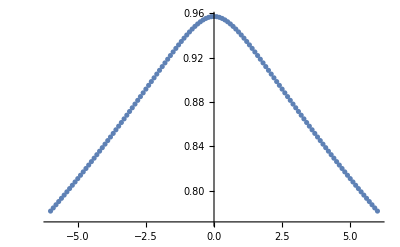

```mathematica
L = {};
Z = {};
For[i=-60,i<=60,i++,
Temp=  1000^(i/100);
temp = i/10;
data= First[NMaximize[{ErrorFun2[e1,2*e1,3*e1,CoherenceTime,td1,TExiton ,temp]},{e1,td1}]];
AppendTo[L,data];
AppendTo[Z,temp]]
ListPlot[Transpose[{Z,L}]]
```

```mathematica
L
```

{0.993358,0.993357,0.993356,0.993355,0.993354,0.993352,0.993351,0.993349,0.993347,0.993345,0.993342,0.993339,0.993335,0.993331,0.993326,0.993321,0.993315,0.993308,0.9933,0.99329,0.993279,0.993267,0.993253,0.993237,0.993218,0.993196,0.993172,0.993143,0.993111,0.993074,0.993031,0.992982,0.992925,0.99286,0.992786,0.992701,0.992603,0.99249,0.992361,0.992213,0.992043,0.991848,0.991624,0.991367,0.991072,0.990734,0.990346,0.989901,0.989391,0.988807,0.988137,0.987369,0.986489,0.985482,0.984329,0.98301,0.981501,0.979777,0.977808,0.97556,0.972997,0.970078,0.966755,0.962978,0.958692,0.953835,0.948342,0.942141,0.935158,0.927313,0.918527,0.908717,0.897802,0.885706,0.872358,0.857698,0.841681,0.824276,0.805479,0.785308,0.763812,0.741071,0.717197,0.692336,0.666663,0.640382,0.613716,0.586909,0.560206,0.533858,0.508106,0.483174,0.459265,0.436557,0.415192,0.395281,0.376901,0.360092,0.344862,0.331191}

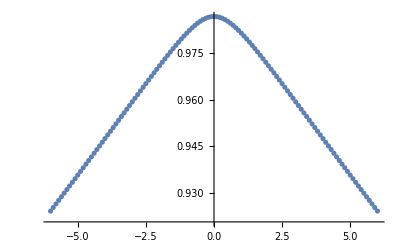

```mathematica
TExiton = 0.4;
CoherenceTime  = 100;
gr = 3;
thetaDot = 2 Pi/1;
L = {};
Z = {};
For[i=-60,i<=60,i++,
Temp=  1000^(i/100);
temp = i/10;
data= First[NMaximize[{ErrorFun2[e1,2*e1,3*e1,CoherenceTime,td1,TExiton ,temp]},{e1,td1}]];
AppendTo[L,data];
AppendTo[Z,temp]]
ListPlot[Transpose[{Z,L}]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

General::stop: Further output of FindMaximum::fmgz will be suppressed during this calculation.

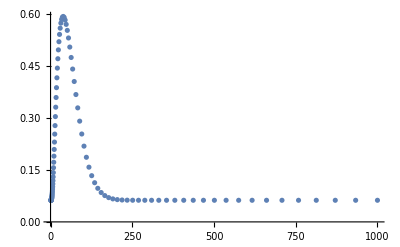

```mathematica
L = {};
Z = {};
For[i=1,i<=100,i++,
Temp=  1000^(i/100);
data= First[FindMaximum[ErrorFun4[e1,e2,e3,e4,e5,CoherenceTime,thetaDot/Temp,TExiton ,gr],{e1,0},{e2,0},{e3,0},{e4,0},{e5,0}]];
AppendTo[L,data];
AppendTo[Z,Temp]]
ListPlot[Transpose[{Z,L}]]
```